# Kriptovalute

## Pripravil : Jure Kovač, FMF 2020/21

Youtube video : “https://www.youtube.com/watch?v=5GHOoF0F8R0&ab_channel=jurekovac”

## Uvodna beseda

Kriptovalute. Za kaj pravzaprav gre? Za nekatere so to tehnologija prihodnosti, za marsikoga enostaven zaslužek spet tretji v kriptovalutah vidijo navaden “nateg”. Večina ljudi pa se pravzaprav ne zanima za to čudo - veliko so smo slišali preko medijev o kriptovalutah leta 2017, ko so kriptovalute doživele nenormalen vzpon (kar je tudi povzročilo mrzlico rudarjenja kriptovalut), ter nedavno januarja 2021, ko so cene le-teh ponovno narasle, na najvišjo možno vsoto (vrednost Bitcoina je znašala skoraj 60.000 eur). A kaj je pravzaprav “kriptovaluta”? Če na hitro opišemo zadevo, bi marsikdo mislil, da gre pravzaprav za neke vrste internetno delnico, mar ne? Ne ravno. V sledečem seminarskem delu, bom poizkušal opisati kriptovalute ter analiziral razvoj, ter si pomagal z orodji, ki jih ponuja Wolframova Mathematica.

## 1. Poglavje - Kripto za nevedneže

## 1. Definicija (Wikipedia)

```mathematica
def =TextSentences[WikipediaData["Cryptocurrency"]][[;;7]]
```

{A cryptocurrency, crypto-currency, or crypto is a digital asset designed to work as a medium of exchange wherein individual coin ownership records are stored in a ledger existing in a form of a computerized database using strong cryptography to secure transaction records, to control the creation of additional coins, and to verify the transfer of coin ownership.,It typically does not exist in physical form (like paper money) and is typically not issued by a central authority.,Cryptocurrencies typically use decentralized control as opposed to a central bank digital currency (CBDC).,When a cryptocurrency is minted or created prior to issuance or issued by a single issuer, it is generally considered centralized.,When implemented with decentralized control, each cryptocurrency works through distributed ledger technology, typically a blockchain, that serves as a public financial transaction database.,Bitcoin, first released as open-source software in 2009, is the first decentralized cryptocurrency.,Since the release of bitcoin, other cryptocurrencies have been created.}

```mathematica
TextTranslation[def,#]&/@{"Slovenian"}
```

{{Kriptovaluta, kriptovaluta ali kripto je digitalno sredstvo, namenjeno za delo kot medij izmenjave, v katerem so posamezni zapisi lastništva kovancev shranjeni v knjigi, ki obstaja v obliki računalniško podprte zbirke podatkov z uporabo močne kriptografije za varno transakcijo, za nadzor nad ustvarjanjem dodatnih kovancev in za preverjanje prenosa lastništva kovancev.,Običajno ne obstaja v fizični obliki (kot papirni denar) in ga običajno ne izda osrednji organ.,Kripto valute običajno uporabljajo decentraliziran nadzor v nasprotju z digitalno valuto centralne banke (CBDC).,Kadar je kripto valuta kovnjena ali ustvarjena pred izdajo ali izdajo enega izdajatelja, se na splošno šteje za centralizirano.,Ko se izvaja z decentraliziranim nadzorom, vsaka kripto valuta deluje s tehnologijo distribuirane knjige, običajno blockchain, ki služi kot javna zbirka podatkov o finančnih transakcijah.,Bitcoin, prvič izdan kot odprtokodna programska oprema leta 2009, je prva decentralizirana kriptokurrenca.,Od izdaje bitcoina so bile ustvarjene druge kriptovate.}}

## 2. Zgodovina (Wikipedia)

```mathematica
his = TextSentences[WikipediaData["Cryptocurrency"]][[9;;24]]
```

{In 1983, the American cryptographer David Chaum conceived an anonymous cryptographic electronic money called ecash.,Later, in 1995, he implemented it through Digicash, an early form of cryptographic electronic payments which required user software in order to withdraw notes from a bank and designate specific encrypted keys before it can be sent to a recipient.,This allowed the digital currency to be untraceable by the issuing bank, the government, or any third party.,In 1996, the National Security Agency published a paper entitled How to Make a Mint: the Cryptography of Anonymous Electronic Cash, describing a Cryptocurrency system, first publishing it in an MIT mailing list and later in 1997, in The American Law Review (Vol. 46, Issue 4).,In 1998, Wei Dai published a description of "b-money", characterized as an anonymous, distributed electronic cash system.,Shortly thereafter, Nick Szabo described bit gold.,Like bitcoin and other cryptocurrencies that would follow it, bit gold (not to be confused with the later gold-based exchange, BitGold) was described as an electronic currency system which required users to complete a proof of work function with solutions being cryptographically put together and published.,In 2009, the first decentralized cryptocurrency, bitcoin, was created by presumably pseudonymous developer Satoshi Nakamoto.,It used SHA-256, a cryptographic hash function, in its proof-of-work scheme.,In April 2011, Namecoin was created as an attempt at forming a decentralized DNS, which would make internet censorship very difficult.,Soon after, in October 2011, Litecoin was released.,It used scrypt as its hash function instead of SHA-256.,Another notable cryptocurrency, Peercoin used a proof-of-work/proof-of-stake hybrid.,On 6 August 2014, the UK announced its Treasury had been commissioned a study of cryptocurrencies, and what role, if any, they could play in the UK economy.,The study was also to report on whether regulation should be considered.,In June 2021, El Salvador became the first country to accept Bitcoin as legal tender, after the Legislative Assembly had voted 62–22 to pass a bill submitted by President Nayib Bukele classifying the cryptocurrency as such.}

```mathematica
TextTranslation[his,#]&/@{"Slovenian"}
```

{{Leta 1983 je ameriški kriptograf David Chaum spočel anonimni kriptografski elektronski denar imenovan ecash.,Kasneje ga je leta 1995 izvajal prek Digicasha, zgodnje oblike kriptografskih elektronskih plačil, ki so zahtevala uporabniška programska oprema, da bi iz banke umaknil zapiske in pred pošiljanje prejemniku določila posebne šifrirane ključe.,To je omogočilo, da se digitalni valuti ni mogoče izslediti s strani banke, vlade ali katere koli tretje osebe.,Leta 1996 je Agencija za nacionalno varnost objavila članek z naslovom How to Make a Mint: the Cryptography of Anonymous Electronic Cash, ki opisuje sistem kripto valut, ki ga je najprej objavil na MIT poštnem seznamu in kasneje leta 1997, v Ameriškem pregledu prava (Vol. 46, Issue 4).,Leta 1998 je Wei Dai objavil opis "b-denarja", značilnega za anonimen, distribuiran elektronski denarni sistem.,Kmalu potem je Nick Szabo opisal bit zlata.,Kot bitcoin in druge kriptovalute, ki bi mu sledile, je bil bit gold (ki se ne sme zamenjati s poznejšim borzo na osnovi zlata, BitGold) opisan kot sistem elektronske valute, ki je od uporabnikov zahteval, da dokončajo dokaz o delovni funkciji z rešitvami, ki se kriptografsko sestavijo in objavijo.,Leta 2009 je prvo decentralizirano kriptoventijo, bitcoin, ustvaril domnevno psevdonimni razvijalec Satoshi Nakamoto.,V svoji shemi za dokaz dela je uporabila SHA-256, kriptografsko funkcijo hasha.,Aprila 2011 je bil Namecoin ustvarjen kot poskus oblikovanja decentraliziranega DNS- ja, kar bi zelo otežujelo cenzuro interneta.,Kmalu zatem, oktobra 2011, je izšel Litecoin.,Uporabil je šifriranje kot svojo funkcijo hash namesto SHA-256.,Peercoin je uporabil še eno cryptocurrency, ki je bila uporabljena kot dokaz za delo/dokaz o kocki.,Združeno kraljestvo je 6.,V študiji je bilo treba poročati tudi o tem, ali je treba preučiti ureditev.,Junija 2021 je El Salvador postal prva država, ki je sprejela Bitcoin kot pravno ponudbo, potem ko je zakonodajna skupščina glasovala 62â22 za sprejetje predloga zakona, ki ga je predložil predsednik Nayib Bukele, ki je kriptovanko opredelil kot tako.}}

Kriptovaluta je torej le neke vrste koda, ki nosi raznorazne podatke o lastništvu, transakcijah itd. Ampak ... zakaj bi kdorkoli sploh želel kaj takega? Saj sploh nima fizične oblike, sploh ni "prava" stvar!
Pa vendarle se moramo isto vprašati o naši stari dobri gotovini ...  Je tudi denar kot ga poznamo "prava" stvar ? Konec koncev gre samo za posebno vrsto papirja ter kovine, le - teh pa je na svetu precej. Ideja vrednosti neke "stvari" je v tem, da ji bo vrednosti narasla po tem, koliko ljudi se pravzaprav zanima za njo. In kot vemo, bi se dan danes marsikdo želel bitcoina. A temu vedno ni bilo tako - prva komercialna transakcija Bitcoina se je izvedla leta 2010. Programer po imenu Laszlo Hanyecz je namreč za menjavo 10.000 Bitcoinov naročil dve pici. Če bi prevedli tak znesek Bitcoinov v današnji čas, bi vrednost le - teh znašala kar 284.420 .000 dolarjev! Definitivno bi si lahko privoščil še tretjo pico. Pa vendar ... že iz zgornjega opisa nam postane jasno, da ni šlo za "napako", ki jo je gospod Hanzecz storil. To dejanje je bilo namreč ključno za nadaljni razvoj Bitcoina in kriptovalut samih, saj je bila prva transakcija kriptovalute za neko materialno "dobrino".

## 3. Bitcoin, Ethereum, Dogecoin

Ena od bolj "kul" zadev kriptovalut je ta, da so “decentralizirane”. Kar to pomeni je, da vlada in banke NE morejo vplivati na to tehnologijo. Še več, veliko kriptovalut je skorajda imunih na inflacijo (npr. Bitcoinov je končno mnogo - 21 milijonov)! Stvar je v tem, da je vsaka enota kriptovalute UNIKATNA. Ker namreč vsaka nosi svojo unikatno kodo z določenimi informacijami. Le-ta se imenuje HASH. 
Poglejmo si 3 kriptovalute, ki so bile v letu 2021 najbolj odmevne.

### 1. Bitcoin

Bitcoin smo omenili že precejkrat - prva kriptovaluta, ustvarjena leta 2009, njen avtor je “Satoshi Nakomoto” (ne ve se, ali je avtor eden ali več, vendar naj bi bilo ime “Satoshi Nakomoto” zgolj psevdonim). Danes je Bitcoin daleč najbolj vredna in zaželjena kriptovaluta na svetu.

#### Tabela - Bitcoin

```mathematica
BlockchainData[BlockchainBase->"Bitcoin"]//Dataset
```

#### Graf cene Bitcoina

```mathematica
ResourceFunction["https://www.wolframcloud.com/obj/antononcube/DeployedResources/Function/CryptocurrencyData"]["BTC"]
```

TimeSeries[…]

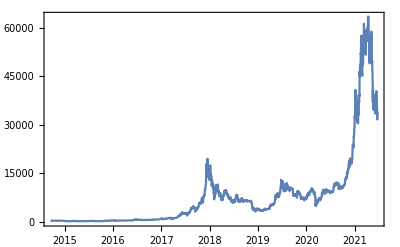

```mathematica
DateListPlot[%,PlotRange->All]
```

### 2. Ethereum

Ideja za Ethereum je “padla” leta 2013, udejanila pa se je leta 2014. Za razliko od Bitcoina, vemo kdo je ustvarjalec Ethereuma - gre namreč za Rusko-Kanadskega programerja po imenu Vitalik Buterin. Za mnoge poznavalce je Vitalik pravo čudo, skoraj prerok na Kripto platformi - nadarjen računalničar je bil namreč star zgolj 20 let, ko je ustvaril Ethereum, ki je danes najbolj aktiven “blockchain” na Kripto-trgu, je decentraliziran, ter sama tehnologija za Ethereumom naj bi bila ena najbolj dovršenih v današnjem času. Po mnenju mnogih strokovnjakov naj bi cena Ethereuma v prihodnosti prerasla ceno Bitcoina (Ethereum je trenutno drugi na lestvici, govori pa se, da je v izdelavi že Ethereum 2.0).

#### Tabela - Etereum

```mathematica
BlockchainData[BlockchainBase->"Ethereum"]//Dataset
```

#### Graf cene Ethereuma

```mathematica
ResourceFunction["https://www.wolframcloud.com/obj/antononcube/DeployedResources/Function/CryptocurrencyData"]["ETH"]
```

TimeSeries[…]

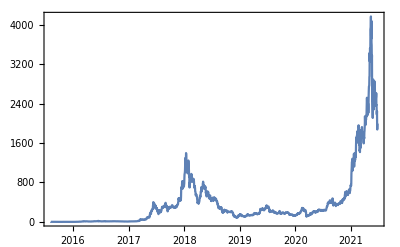

```mathematica
DateListPlot[%,PlotRange->All]
```

### 3. Dogecoin

Tale pa je malo drugačen. “Dogecoin” je namreč kriptovaluta, ki je nastala leta 2013 pod prsti Billy-ja Markus-a, ter Jackson-a Palmer-ja. Kar je zanimivo pri Dogecoinu je to, da je njegov nastanek praktična šala. Ideja za Dogecoin izvira iz internetne šale, kjer je na sliki psiček pasme Shiba Inu s prekrižanimi tačkami. Ta “meme” po imenu Doge (izpeljanka iz angleške besede Dog) je še danes precej v uporabi, zaradi česar tudi pripisujejo vzpon te Kriptovalute -  Dogecoin je namreč iz decembra leta 2020 do začetka maja 2021 (torej v slabih 5. mesecih) narasel iz 0,004 eur na 0,72 eur. Sicer se ne sliši nič posebnega, glede na to, da cena posameznega žetona ni dosegla niti 1 eur, a če bi pred decembrom 2020 v Dogecoin vložili 10 eur, bi vam to prineslo kar 1800 eur - torej 1790 eur čistega zaslužka! Kakorkoli, ker je bil Dogecoin narejen kot šala, je tudi tehnologija za njim praktično neuporabna. Poleg tega se lahko Dogecoinov ustvari neskončno mnogo, kar pomeni, da ni zaščiten pred inflacijo (pravzaprav je fizični denar bolj zaščiten pred inflacijo kot Dogecoin sam).

#### Tabela - Dogecoin

```mathematica
BlockchainData[BlockchainBase->"Dogecoin"]//Dataset
```

BlockchainData::bbase: Invalid BlockchainBase specification Dogecoin.

Dataset`ExtractRawData::dataextr: Data extraction failed.

Dataset[$Failed]

Iz neznanega razloga tukaj funkcija ne deluje.

#### Graf cene Dogecoina

```mathematica
ResourceFunction["https://www.wolframcloud.com/obj/antononcube/DeployedResources/Function/CryptocurrencyData"]["DOGE"]
```

TimeSeries[…]

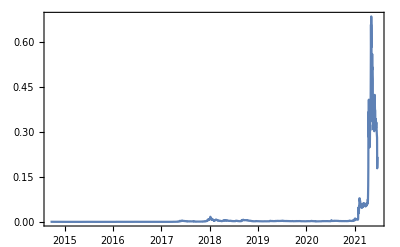

```mathematica
DateListPlot[%,PlotRange->All]
```

#### Primerjava Bitcoina, Ethereuma ter Dogecoina

```mathematica
ResourceFunction["https://www.wolframcloud.com/obj/antononcube/DeployedResources/Function/CryptocurrencyData"][{"BTC","ETH", "DOGE"}]
```

<|BTC→TimeSeries[…],ETH→TimeSeries[…],DOGE→TimeSeries[…]|>

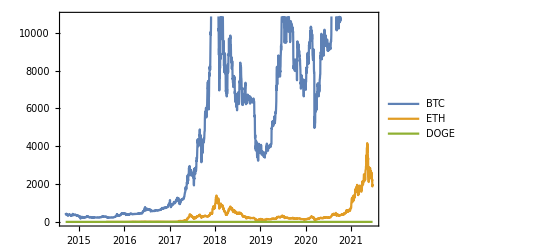

```mathematica
DateListPlot[%]
```

## Normaliziran pogled

V sledeči analizi bom predstavil vrednosti Bicoina, Ethereuma in Dogecoina v normaliziranem pogledu - to pomeni, da bo izhodiščna (začetna vrednost) predstavljena z 1, sledeče vrednosti pa glede na spreminjanje le - te.

### 1. Bitcoin

```mathematica
DataBit = ResourceFunction["https://www.wolframcloud.com/obj/antononcube/DeployedResources/Function/CryptocurrencyData"]["BTC"]//Normal;
```

```mathematica
DatumiBit = Table[DataBit[[i]][[1]],{i,1,Length[DataBit]}];
```

```mathematica
VrednostiBit = Table[DataBit[[i]][[2]],{i,1,Length[DataBit]}];
```

```mathematica
VrednostiBitNormirane = VrednostiBit/VrednostiBit[[1]];
```

```mathematica
TimeSeries[VrednostiBitNormirane,{DatumiBit}]
```

TimeSeries[…]

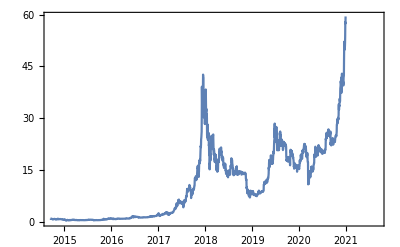

```mathematica
DateListPlot[%22]
```

### 2. Ethereum

```mathematica
DataEth=ResourceFunction["https://www.wolframcloud.com/obj/antononcube/DeployedResources/Function/CryptocurrencyData"]["ETH"]//Normal;
```

```mathematica
DatumiEth = Table[DataEth[[i]][[1]],{i,1,Length[DataEth]}];
```

```mathematica
VrednostiEth = Table[DataEth[[i]][[2]],{i,1,Length[DataEth]}];
```

```mathematica
VrednostiEthNormirane = VrednostiEth/VrednostiEth[[1]];
```

```mathematica
TimeSeries[VrednostiEthNormirane,{DatumiEth}]
```

TimeSeries[…]

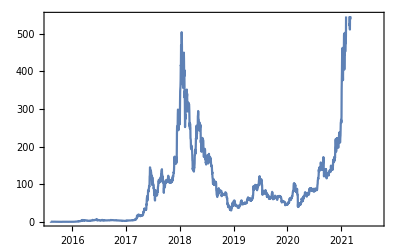

```mathematica
DateListPlot[%7]
```

### 3. Dogecoin

```mathematica
DataDoge=ResourceFunction["https://www.wolframcloud.com/obj/antononcube/DeployedResources/Function/CryptocurrencyData"]["DOGE"]//Normal;
```

```mathematica
DatumiDoge = Table[DataDoge[[i]][[1]],{i,1,Length[DataDoge]}];
```

```mathematica
VrednostiDoge = Table[DataDoge[[i]][[2]],{i,1,Length[DataDoge]}];
```

```mathematica
VrednostiDogeNormirane = VrednostiDoge/VrednostiDoge[[1]];
```

```mathematica
TimeSeries[VrednostiDogeNormirane,{DatumiDoge}]
```

TimeSeries[…]

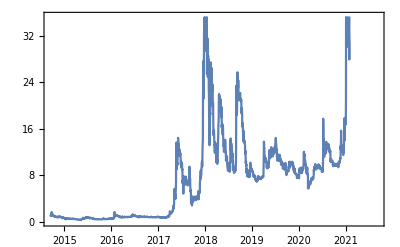

```mathematica
DateListPlot[%13]
```

## Model linearne regresijske premice

### 1. Bitcoin

```mathematica
Bit = ResourceFunction["https://www.wolframcloud.com/obj/antononcube/DeployedResources/Function/CryptocurrencyData"]["BTC"];
```

```mathematica
ModelBit = LinearModelFit[Bit,x,x];
```

```mathematica
ModelBit["BestFit"];
```

```mathematica
Plot[-532054.012938574+0.00014500086334580338 x,{x,-5.503974259136431*^9,5.503974259136431*^9}];
```

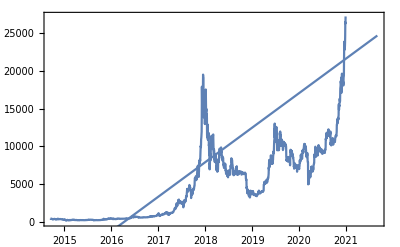

```mathematica
Show[DateListPlot[Bit], Plot[ModelBit["BestFit"],{x,AbsoluteTime[{2014, 12, 1}], AbsoluteTime[{2021, 9, 1}]}] ]
```

### 2. Ethereum

```mathematica
Eth = ResourceFunction["https://www.wolframcloud.com/obj/antononcube/DeployedResources/Function/CryptocurrencyData"]["ETH"];
```

```mathematica
ModelEth= LinearModelFit[Eth,x,x];
```

```mathematica
ModelEth["BestFit"];
```

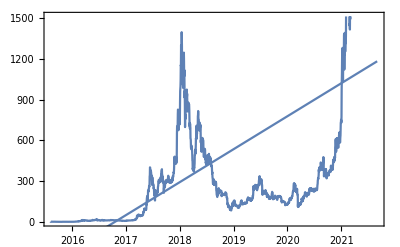

```mathematica
Show[DateListPlot[Eth], Plot[ModelEth["BestFit"],{x,AbsoluteTime[{2014, 12, 1}], AbsoluteTime[{2021, 9, 1}]}] ]
```

### 3. Dogecoin

```mathematica
Doge = ResourceFunction["https://www.wolframcloud.com/obj/antononcube/DeployedResources/Function/CryptocurrencyData"]["DOGE"];
```

```mathematica
ModelDoge= LinearModelFit[Doge,x,x];
```

```mathematica
ModelDoge["BestFit"];
```

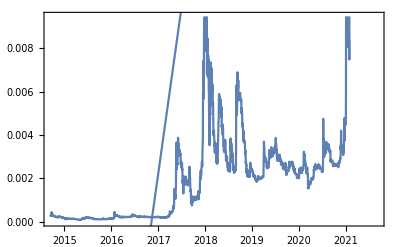

```mathematica
Show[DateListPlot[Doge], Plot[ModelDoge["BestFit"],{x,AbsoluteTime[{2014, 12, 1}], AbsoluteTime[{2021, 9, 1}]}] ]
```

## 2. Poglavje - Podrobna analiza

V tem poglavju bom bolj natančno izkoristil orodje Mathematice za podrobno analizo

## 1. Pridobitev in predstavitev osnovnih podatkov v obliki tabele

#### Pridobimo podatke kriptovalut iz strani Yahoo! Finance

```mathematica
AbsoluteTiming[lsData=Import["https://finance.yahoo.com/cryptocurrencies","Data"];]
```

{5.33667,Null}

#### Določimo, kje se podatki nahajajo

```mathematica
pos=First@Position[lsData,{"Symbol","Name","Price (Intraday)","Change","% Change",___}];
dsCryptoCurrenciesColumnNames=lsData[[Sequence@@pos]]
Length[dsCryptoCurrenciesColumnNames]
```

{Symbol,Name,Price (Intraday),Change,% Change,Market Cap,Volume in Currency (Since 0:00 UTC),Volume in Currency (24Hr),Total Volume All Currencies (24Hr),Circulating Supply,52 Week Range,1 Day Chart}

12

#### Pridobitev podatkov

```mathematica
dsCryptoCurrencies=lsData[[Sequence@@Append[Most[pos],2]]];
Dimensions[dsCryptoCurrencies]
```

{25,10}

#### Ustvarimo obsežno tabelo kriptovalut ter raznoraznih informacij o le-teh

```mathematica
dsCryptoCurrencies=Dataset[dsCryptoCurrencies][All,AssociationThread[dsCryptoCurrenciesColumnNames[[1;;-3]],#]&]
```

## 2. Podrobna analiza

#### Pridobitev/pretvorba imen

```mathematica
ResourceFunction["https://www.wolframcloud.com/obj/antononcube/DeployedResources/Function/CryptocurrencyData"]["CryptocurrencyNames"]
```

<|BTC→Bitcoin,ETH→Ethereum,USDT→Tether,BNB→BinanceCoin,ADA→Cardano,XRP→XRP,USDC→Coin,DOGE→Dogecoin,DOT1→Polkadot,HEX→HEX,UNI3→Uniswap,BCH→BitcoinCash,LTC→Litecoin,LINK→Chainlink,SOL1→Solana,MATIC→MaticNetwork,THETA→THETA,XLM→Stellar,VET→VeChain,ICP1→InternetComputer,ETC→EthereumClassic,TRX→TRON,FIL→FilecoinFutures,XMR→Monero,EOS→EOS|>

#### Predstavitev Bitcoin in Ethereuma iz “Financial Data” - vrednost v dolarjih tekom leta 2021

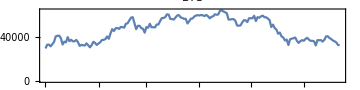
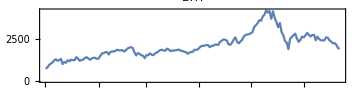

```mathematica
Row[DateListPlot[FinancialData[#,"Jan 1 2021"],ImageSize->Medium,AspectRatio->1/4,PlotLabel->#]&/@{"BTC","ETH"}]
```

#### Povzetek v tabeli

```mathematica
dsCCSummary=ResourceFunction["https://www.wolframcloud.com/obj/antononcube/DeployedResources/Function/CryptocurrencyData"][All,"Summary"]
```

#### Manipulacija podatkov iz tabele - ureditev po kategorijah

```mathematica
ResourceFunction["RecordsSummary"][dsCCSummary]
```

{1 Symbol
ADA-USD | 1
BCH-USD | 1
BNB-USD | 1
BTC-USD | 1
DOGE-USD | 1
DOT1-USD | 1
(Other) | 19,2 Name
BinanceCoin USD | 1
BitcoinCash USD | 1
Bitcoin USD | 1
Cardano USD | 1
Chainlink USD | 1
Dogecoin USD | 1
(Other) | 19,3 Price (Intraday)
Min | 0.055459
1st Qu | 0.909739
Median | 16.03
3rd Qu | 72.7325
Mean | 1493.86
Max | 34016.3,4 Change
Min | -0.001486
1st Qu | 0.0323818
Median | 1.08
3rd Qu | 7.7825
Mean | 105.352
Max | 2401.55,5 % Change
Min | -0.0177
1st Qu | 0.0599
Median | 0.0942
Mean | 0.094948
3rd Qu | 0.125175
Max | 0.2948,6 Market Cap
Min | 3.496×10^9
1st Qu | 4.9425×10^9
Median | 8.629×10^9
3rd Qu | 2.8534×10^10
Mean | 4.89524×10^10
Max | 6.37503×10^11,7 Volume in Currency (Since 0:00 UTC)
Min | 2.5868×10^7
1st Qu | 1.09162×10^9
Median | 2.599×10^9
3rd Qu | 4.7745×10^9
Mean | 1.0192×10^10
Max | 1.04668×10^11,8 Volume in Currency (24Hr)
Min | 2.5868×10^7
1st Qu | 1.09162×10^9
Median | 2.599×10^9
3rd Qu | 4.7745×10^9
Mean | 1.0192×10^10
Max | 1.04668×10^11,9 Total Volume All Currencies (24Hr)
Min | 2.5868×10^7
1st Qu | 1.09162×10^9
Median | 2.599×10^9
3rd Qu | 4.7745×10^9
Mean | 1.0192×10^10
Max | 1.04668×10^11,10 Circulating Supply
Min | 1.7938×10^7
1st Qu | 1.16384×10^8
Median | 9.54346×10^8
Mean | 2.5601×10^10
3rd Qu | 3.55208×10^10
Max | 1.73411×10^11}

#### Nedavni dogodki, povezani z Kripto platformo

```mathematica
lsEventData={{"Jun 18, 2021","China to shut down over 90% of its Bitcoin mining capacity after local bans","https://www.globaltimes.cn/page/202106/1226598.shtml"},{"Jun 10, 2021","Global banking regulators call for toughest rules for cryptocurrencies","https://www.theguardian.com/technology/2021/jun/10/global-banking-regulators-cryptocurrencies-bitcoin"},{"June 10, 2021","IMF sees legal, economic issues with El Salvador's bitcoin move","https://www.reuters.com/business/finance/imf-sees-legal-economic-issues-with-el-salvador-bitcoin-move-2021-06-10/"},{"June 8, 2021","El Salvador Becomes First Country To Adopt Bitcoin as Legal Tender After Passing Law","https://www.cnbc.com/2021/06/09/el-salvador-proposes-law-to-make-bitcoin-legal-tender.html"},{"June 8, 2021","US recovers millions in cryptocurrency paid to Colonial Pipeline ransomware hackers","https://edition.cnn.com/2021/06/07/politics/colonial-pipeline-ransomware-recovered/"},{"June 4, 2021","Start of Bitcoin 2021: World's Largest Cryptocurrency Conference Coming To Wynwood","https://miami.cbslocal.com/2021/06/04/bitcoin-2021-worlds-largest-cryptocurrency-conference-coming-to-wynwood/"},{"June 6, 2021","End of Bitcoin 2021: World's Largest Cryptocurrency Conference Coming To Wynwood","https://miami.cbslocal.com/2021/06/04/bitcoin-2021-worlds-largest-cryptocurrency-conference-coming-to-wynwood/"},{"May 28, 2021","Iran Bans Crypto Mining After Months of Blackouts","https://gizmodo.com/iran-bans-crypto-mining-after-months-of-blackouts-1846991039"},{"May 19, 2021","Bitcoin, Ethereum prices in free fall as China plans crackdown on mining and trading","https://www.cnet.com/news/bitcoin-ethereum-prices-in-freefall-as-china-plans-crackdown-on-mining-and-trading/#ftag=CAD590a51e"}};
dsEventData=Dataset[lsEventData][All,AssociationThread[{"Date","Event","URL"},#]&];
dsEventData=dsEventData[All,Join[Prepend[#,"DateObject"->DateObject[#Date]],<|"URL"->URL[#URL]|>]&];
dsEventData=dsEventData[SortBy[#DateObject&]]
```

## Zaključna beseda

Kot lahko vidimo, je tehnologija kriptovalut še vedno nekoliko zapletena in nejasna - izgleda, da smo še nekoliko daleč od bolj splošne uporabe kriptovalut med večjo množico, le čas pa bo pokazal, ali gre resnično za tehnologijo prihodnosti, ki bo zamenjala gotovino in denar kot tak, ali pa se bo izkazalo, da so skeptiki imeli ves čas prav.